# Further Series and Iterative Methods

## Accompanies Section 1.5 of Experimental Mathematics: A Computational Perspective by Matthew P. Richey and Matthew L. Wright

## Ramanujan’s Formula

Here is Ramanujan’s formula, from equation (1.12) in the text:

We will write a module that adds up m+1 terms (indexes k=0,...,m) of this sum. Since the formula gives an approximation to 1/π, we must invert the result to obtain an approximation to π. The following module includes a print statement that prints each term of the sum, which is helpful for testing the code and confirming that it works as expected.

```mathematica
ramanujan[m_]:=Module[{total=0, val},
Do[
val=((4k)!(1103+26390k))/((k!)^4*396^(4k));
Print[val];
total+=val,
{k,0,m}];
total*=2Sqrt[2]/9801;
1/total (* return value *)
]
```

Try it with just one term (m=0). Note that the code prints 1103 since this is the value of the first term.

```mathematica
N[ramanujan[0],20]
```

1103

3.1415927300133056603

Now try it with two terms. Note that the fraction that appears in the output is the value of the k=1 term of the sum.

```mathematica
N[ramanujan[1],20]
```

1103

27493/1024635744

3.141592653589793878

It looks like our code works. Now we can remove the print statement and run the code with more terms. The following copy of the module has the print statement commented out.

```mathematica
ramanujan[m_]:=Module[{total=0, val},
Do[val=((4k)!(1103+26390k))/((k!)^4*396^(4k));
(*Print[val];*)
total+=val,
{k,0,m}];
total*=2Sqrt[2]/9801;
1/total (* return value *)
]
```

Let's run the module for each value of m from 0 to 10 and collect the results in a list. The /@ shorthand for the Map function is convenient for this.

```mathematica
piValues=ramanujan/@Range[0,10];
piValues
```

{9801/(2206 √2),(2510613731736 √2)/1130173253125,(2286635172367940241408 √2)/1029347477390786609545,(17252765328978109815564789153792 √2)/7766473062254307011793347201855,(1131379202490552979877435552947122965839872 √2)/509299577881529611662930757403081523769055,(128805730098892711723125911845114081418091536842752 √2)/57982950211280781944919792648021104999982386829481,(7774760263562699859971501015139525269727219309055349184528384 √2)/3499871759747710499842768988784507373816789022688631739047925,(885144140786355895741177195716026970950416670420565960985448225439744 √2)/398454856050409400033667498427037929849361304439288784703764447270125,(14071471712843535798792494970078253119671801362717159118900747103370578550063104 √2)/6334387787708107824222495376281706107615730472323276284056009760393364218543125,(31532456625322022370765818276612583919584083811310999597255056965804073403194963043194765312 √2)/14194592594146827909170805406080156403980453284185387917579020073045561359013099552859053125,(258474257235476477051634224477005861793643791092488013501737085215352314477706263478530979938932097024 √2)/116354295547844200479625540962705305445031010498388307062857519290687784871920308555177681218916232885}

We can also print the approximations to many decimal places:

```mathematica
N[piValues ,60]
```

{3.14159273001330566031399618902521551859958160711003355965654,3.14159265358979387799890582630601309421664502932284887917396,3.1415926535897932384626490657027588981566774804623347811684,3.1415926535897932384626433832795552731599742104203799112167,3.14159265358979323846264338327950288419766381813303062397617,3.14159265358979323846264338327950288419716939937984683274351,3.14159265358979323846264338327950288419716939937510582102093,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494}

### Accuracy

Let’s compute the accuracy of each approximation using the log_10 method. Ramanujan’s method produces so many correct digits that we need to tell Mathematica to use extra precision for this calculation. (Otherwise, Mathematica will show an “Internal precision limit reached” message.)

```mathematica
accuracyRamanujan=Block[{$MaxExtraPrecision=1000},N[-Log[10,Abs[Pi-piValues]],5]]
```

{7.1168,15.194,23.245,31.281,39.306,47.324,55.337,63.347,71.353,79.357,87.36}

We can also print the approximations and their accuracy as a table, similar to Table 1.6 in the text.

```mathematica
TableForm[Transpose[{Range[0,10],N[piValues,50],accuracyRamanujan}],TableHeadings->{None,{"m","approximation","accuracy"}}]
```

m | approximation | accuracy
0 | 3.14159273001330566031399618902521551859958160711 | 7.1168
1 | 3.1415926535897938779989058263060130942166450293228 | 15.194
2 | 3.1415926535897932384626490657027588981566774804623 | 23.245
3 | 3.1415926535897932384626433832795552731599742104204 | 31.281
4 | 3.141592653589793238462643383279502884197663818133 | 39.306
5 | 3.1415926535897932384626433832795028841971693993798 | 47.324
6 | 3.1415926535897932384626433832795028841971693993751 | 55.337
7 | 3.1415926535897932384626433832795028841971693993751 | 63.347
8 | 3.1415926535897932384626433832795028841971693993751 | 71.353
9 | 3.1415926535897932384626433832795028841971693993751 | 79.357
10 | 3.1415926535897932384626433832795028841971693993751 | 87.36

It appears that the Ramanujan algorithm adds about 8 digits of accuracy for each additional term of the sum.

## Salamin-Brent Algorithm

The following module implements Algorithm 1.23 in the text. 
First we initialize the values a_0=1, b_0=1/(√2), and s_0=1/2. 
Then iterate the following steps for k=1,2,...,m:
a_k=(a_(k-1)+b_(k-1))/2,
b_k=√(a_(k-1)b_(k-1)),
s_k=s_(k-1)-2^k(a_k^2-b_k^2),
p_k=(2 a_k^2)/s_k. 
The value p_m gives an approximation to π.
Note that the following code uses indexed variables instead of the subscripted variables that appear in Algorithm 1.23 in the text.

```mathematica
salaminBrent[m_]:=Module[
(* local variables: declare just the "head" of each indexed variable *)
{a,b,s,p},

(* initialize values *)
a[0]=1;
b[0]=1/Sqrt[2];
s[0]=1/2;

(* main loop *)
Do[
a[k]=(a[k-1]+b[k-1])/2;
b[k]=Sqrt[a[k-1]*b[k-1]];
s[k]=s[k-1]-2^k*(a[k]^2-b[k]^2);
p[k]=2a[k]^2/s[k],
{k,1,m}
];

p[m] (* return value *)
]
```

Try out the module for a small parameter value, and note that it returns an exact expression.

```mathematica
salaminBrent[1]
```

(1+1/(√2))^2/(2 (1/2-2 (-1/(√2)+1/4 (1+1/(√2))^2)))

We can also convert the result to a decimal number.

```mathematica
N[salaminBrent[1],20]
```

3.1876726427121086272

We see that with m=1 we only get one correct digit of π past the decimal point. Let’s run the algorithm again for each m up to 10 and print decimal versions of the approximations we compute

```mathematica
piValues=salaminBrent/@Range[10];
N[piValues,60]
```

{3.18767264271210862720192997052536923265105357185936922648763,3.14168029329765329391807042456000938279571943881540283264419,3.1415926538954464960029147588180434861088792372613115896511,3.14159265358979323846636060270663132175770241134242935648685,3.1415926535897932384626433832795028841971699491647266058347,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494,3.14159265358979323846264338327950288419716939937510582097494}

It looks like we have a lot of correct digits of π after just a few iterations! Let’s compute the accuracy of each approximation. We’ll use the log_10 method as usual. We also need to tell Mathematica to use extra digits of precision for this calculation.

```mathematica
accuracySalminBrent=Block[{$MaxExtraPrecision=10000},N[-Log[10,Abs[Pi-piValues]],5]]
```

{1.3365,4.0573,9.5148,20.43,42.26,85.92,173.24,347.88,697.16,1395.7}

We computed 1395 correct digits of π! It looks like the number of correct digits approximately doubles with each iteration.

We will print our results as a table, similar to Table 1.7 in the text.

```mathematica
TableForm[Transpose[{Range[10],N[piValues,60],accuracySalminBrent}],TableHeadings->{None,{"m","approximation","accuracy"}}]
```

m | approximation | accuracy
1 | 3.18767264271210862720192997052536923265105357185936922648763 | 1.3365
2 | 3.14168029329765329391807042456000938279571943881540283264419 | 4.0573
3 | 3.1415926538954464960029147588180434861088792372613115896511 | 9.5148
4 | 3.14159265358979323846636060270663132175770241134242935648685 | 20.43
5 | 3.1415926535897932384626433832795028841971699491647266058347 | 42.26
6 | 3.14159265358979323846264338327950288419716939937510582097494 | 85.92
7 | 3.14159265358979323846264338327950288419716939937510582097494 | 173.24
8 | 3.14159265358979323846264338327950288419716939937510582097494 | 347.88
9 | 3.14159265358979323846264338327950288419716939937510582097494 | 697.16
10 | 3.14159265358979323846264338327950288419716939937510582097494 | 1395.7

We will also plot the accuracy.

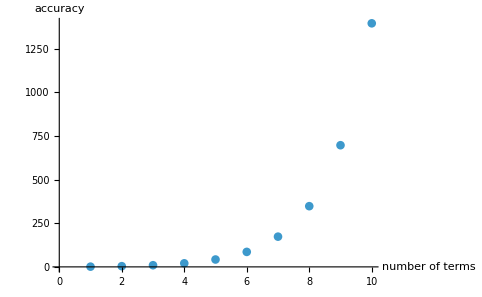

```mathematica
ListPlot[accuracySalminBrent,AxesLabel->{"number of terms","accuracy"}]
```

If the accuracy doubles with each iteration, then the plot above has a shape like 2^n. In this case, a log_2 transform of the data points should result in a linear plot. Let’s plot the log_2 of each data point:

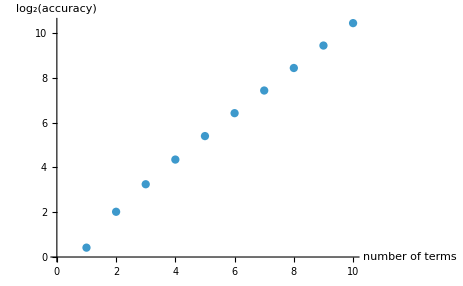

```mathematica
ListPlot[Log[2,accuracySalminBrent],AxesLabel->{"number of terms","log_2(accuracy)"}]
```

This plot looks quite close to linear, which provides good evidence that the accuracy values grow like 2^n.